# Graphics[...] to SVG converter

## Overview

This document collects various functions that I have developed to convert a general Mathematica Graphics object into SVG. It is very much a work in progress, but it shows the approach that I took. The general flow in this converter is that the user provides a Graphics[data] object, and an association with key-value pairs corresponding to SVG attributes is built up. Finally there is a function that takes such an association and generates an SVG string from it.

#### Defaults

When Graphics is used without options, Mathematica uses a set of standard settings for colors, font, opacity etc. These are stored in a global variable defined in the “Defaults” section.

#### convertProperty

Primitives can be styled in Mathematica with properties like EdgeColor, FaceColor and so on. In SVG primitives are also styled with such properties, known in SVG as “attributes”. The function convertProperty generates key-value pairs for attributes from Mathematica properties. All the definitions for convertProperty are gathered in the convertProperty section.

#### convertPrimitive

Mathematica supports various primitives like Rectangle, Circle and so on. Some of these primitives have direct equivalents in SVG, others not. The job of the function convertPrimitive is to take a Mathematica primitive and generate the information necessary to create an equivalent graphics object in SVG. It does not create the actual SVG string, but gathers the information in an Association from which an SVG string can be generated later.

#### Utility functions

The previous sections described convertProperty and convertPrimitive which is where the majority of effort in developing the converter will have to be spent. This is where all the definitions for all the primitives and properties will have to be added. However, there also needs to be functions that can walk through graphics directives and utilize convertProperty and convertPrimitive into SVG strings. These functions are gathered in the section “Utility functions”.

#### Example

This is an example of how far I have come. Note that I still appear to have (I say “appear” because I haven’t worked on it for months, and do not remember exactly all the problems that I still have) probems with the border of the objects in the generated SVG.

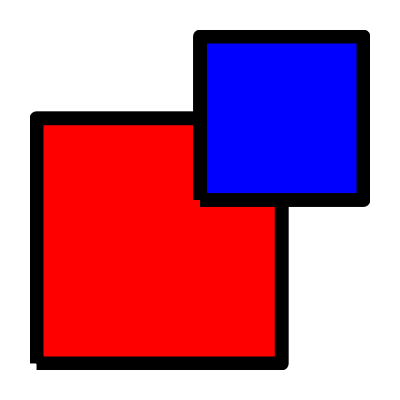

```mathematica
gr=Graphics[{
EdgeForm[{Black,AbsoluteThickness[10]}],
Red,Rectangle[{0,0},{30,30},RoundingRadius->0.5],
Blue,Rectangle[{20,20},{40,40}]
}]
```

```mathematica
str=SVG[gr]
```

{<|type→rect,xmax→30,ymax→0,xmin→0,ymin→-60|>,<|type→rect,xmax→40,ymax→-20,xmin→20,ymin→-60|>}

<svg viewBox="0.0 -48.0 32.0 48.0" preserveAspectRatio="xMinYMin meet" width="348px" height="348px">
	<rect EdgeColor="GrayLevel[0]" FaceColor="GrayLevel[0]" Arrowheads="0.04" EdgeDashing="None" Thickness="Medium" Opacity="1" FontColor="Black" FontFamily="Arial" transform="{}" stroke="rgb(0%,0%,0%)" stroke-width="10pt" fill="rgb(100%,0%,0%)" x="0pt" y="-30pt" width="30pt" height="30pt" rx="0.5pt" ry="0.5pt" />
	<rect EdgeColor="GrayLevel[0]" FaceColor="GrayLevel[0]" Arrowheads="0.04" EdgeDashing="None" Thickness="Medium" Opacity="1" FontColor="Black" FontFamily="Arial" transform="{}" stroke="rgb(0%,0%,0%)" stroke-width="10pt" fill="rgb(0%,0%,100%)" x="20pt" y="-40pt" width="20pt" height="20pt" rx="0pt" ry="0pt" />
</svg>

```mathematica
SystemOpen@Export["test.svg",SVG[gr],"Text"];
```

## Defaults

```mathematica
defaults=<|
"EdgeColor"->Black,
"FaceColor"->Black,
"Arrowheads"->0.04,
"EdgeDashing"->None,
"Thickness"->Medium,
"Opacity"->1,
"FontColor"->"Black",
"FontFamily"->"Arial",
"transform"->{}
|>;
```

```mathematica
ColorQ@GrayLevel@1
```

True

## convertProperty

```mathematica
convertProperty[c:(_RGBColor|_GrayLevel)]:=<|"fill"->convertColor[c]|>
convertProperty[c:(_RGBColor|_GrayLevel),"face"]:=<|"fill"->convertColor[c]|>
convertProperty[c:(_RGBColor|_GrayLevel),"edge"]:=<|"stroke"->convertColor[c]|>

convertProperty[d:AbsoluteDashing[_]]:=convertPrimitive[AbsoluteDashing[{d,d}]]
convertProperty[AbsoluteDashing[d_List]]:=<|
"stroke-dasharray"->StringJoin@@Riffle[ToString[#]<>"pt"&/@d,","]
|>

convertProperty[AbsoluteThickness[d_],_]:=<|"stroke-width"->ToString[d]<>"pt"|>

convertProperty[FaceForm[dir_]]:=Association@@(convertProperty[#,"face"]&/@dir)
convertProperty[EdgeForm[dir_]]:=Association@@(convertProperty[#,"edge"]&/@dir)
```

## convertPrimitive

```mathematica
convertPrimitive[Rectangle[pt:_,patt:OptionsPattern[]],assoc_]:=convertPrimitive[Rectangle[pt,pt+1,patt],assoc]
convertPrimitive[r:Rectangle[_,_,OptionsPattern[]],assoc_]:=Block[{Rectangle},
Rectangle[{xmin_,ymin_},{xmax_,ymax_},OptionsPattern[{RoundingRadius->0}]]:=<|
"meta"-><|
"type"->"rect",
"xmax"->xmax,
"ymax"->-ymin,
"xmin"->xmin,
"ymin"->-ymax-(ymax-ymin)
|>,
"x"->toPt@xmin,
"y"->toPt[-ymax],
"width"->toPt[xmax-xmin],
"height"->toPt[ymax-ymin],
"rx"->toPt@OptionValue[RoundingRadius],
"ry"->toPt@OptionValue[RoundingRadius]
|>;
r
]
```

## Utility functions

### Walk Graphics[...]

```mathematica
getPrimitives[Graphics[data_],defaults_]:=First@Last@Reap@Fold[cumulativeProperties,defaults,data]
```

```mathematica
cumulativeProperties[assoc_,el_]:=Which[
isPrimitive[el],Sow@<|assoc,convertPrimitive[el,assoc]|>;
<|assoc,<|"transform"->{}|>|>,
isTransform[el],cumulativeProperties[
<|assoc,<|"transform"->Append[assoc["transform"],Rest@el]|>|>,
First@el
],
True,<|assoc,convertProperty@el|>
]
```

cumulativeProperties should be called recursively on an Graphics object. Each time it is called it will handle one element of list in Graphics[{list}]. If it encounters a property it will add it to the property list. If it finds a primitive it will use the list of properties it has gathered thus far to sow an SVG string corresponding to that primitive. If the primitive is wrapped in a transform it will also handle that. It is called “cumulativeProperties” because it parses properties just like Mathematica: all properties affect all primitives that come afterwards, new properties overwrite older properties. Example:

```mathematica
getPrimitives[Graphics[{
Red,Rectangle[{0,0},RoundingRadius->0.1],
EdgeForm[Directive[White]],Blue,Rectangle[{0.5,0.5}]
}],defaults]//Column
```

<|EdgeColor→GrayLevel[0],FaceColor→GrayLevel[0],Arrowheads→0.04,EdgeDashing→None,Thickness→Medium,Opacity→1,FontColor→Black,FontFamily→Arial,transform→{},fill→rgb(100%,0%,0%),meta→<|type→rect,xmax→1,ymax→0,xmin→0,ymin→-2|>,x→0pt,y→-1pt,width→1pt,height→1pt,rx→0.1pt,ry→0.1pt|>
<|EdgeColor→GrayLevel[0],FaceColor→GrayLevel[0],Arrowheads→0.04,EdgeDashing→None,Thickness→Medium,Opacity→1,FontColor→Black,FontFamily→Arial,transform→{},fill→rgb(0%,0%,100%),stroke→rgb(100%,100%,100%),meta→<|type→rect,xmax→1.5,ymax→-0.5,xmin→0.5,ymin→-2.5|>,x→0.5pt,y→-1.5pt,width→1.0pt,height→1.0pt,rx→0pt,ry→0pt|>

### Generate SVG

```mathematica
getViewBox[primitives_]:=Module[{meta,minmax},
meta=Through[primitives["meta"]];Print[meta];
minmax=MinMax@*Flatten/@Transpose[{{#xmax,#xmin},{#ymax,#ymin}}&/@meta];
StringTemplate["viewBox=\"`1` `2` `3` `4`\""][
nPtToPx@minmax[[1,1]](* originx: min x*),
nPtToPx@ minmax[[2,1]](* originy: min y *),
nPtToPx[minmax[[1,2]]-minmax[[1,1]]](* width: max x - min x*),
nPtToPx[minmax[[2,2]]-minmax[[2,1]]](* height: max y - min y *)
]
]
```

```mathematica
AssocToSVG[assoc_]:=Module[{data},
data=KeyValueMap[StringTemplate["`1`=\"`2`\""],KeyDrop[assoc,"meta"]];
StringJoin[
"<",assoc["meta","type"]," ",
Sequence@@Riffle[data," "],
" />"
]
]
```

```mathematica
SVG[gr_Graphics]:=StringJoin[
"<svg ",
getViewBox@getPrimitives[gr,defaults],
" preserveAspectRatio=\"xMinYMin meet\" width=\"348px\" height=\"348px\">\n\t",
StringRiffle[AssocToSVG/@getPrimitives[gr,defaults],"\n\t"],
"\n</svg>"
]
```

### is?

```mathematica
isPrimitive[el_]:=MemberQ[{
Rectangle,
Circle
},Head@el]
```

```mathematica
isTransform[el_]:=MemberQ[{
Rotate,
Translate,
Scale
},Head@el]
```

### Convert properties

```mathematica
convertColor[RGBColor[r_,g_,b_]]:=StringTemplate["rgb(`1`%,`2`%,`3`%)"][100r,100g,100b]
convertColor[GrayLevel[gl_]]:=StringTemplate["rgb(`1`%,`1`%,`1`%)"][100gl]
```

```mathematica
toPt[val_]:=StringTemplate["`1`pt"][val]
nPtToPx[val_]:=val/1.25
```